# A 1D study of Adaptive Mesh Refinement in Neural Networks for PDE solving

Gianni Tallarita

In this post I construct an adaptive mesh refined solver for Burgers’ equation over a one-dimensional domain. This is part of a research direction I am exploring in order to implement AMR Numerical PDE solvers on GPUs, within Wolfram Language. As an introduction, I present the standard method of solving this system, along with its known failures, using a static uniform grid and a Runge-Kutta time evolver. To overcome the limitations this solver presents, we introduce adaptive mesh refinement (AMR) in the system. I then demonstrate explicitly the construction of the AMR solver in Neural Network language in order to pass the calculation to GPUs. Finally, I conclude with the limitations of this system and the natural directions of further work this topic screams for.

The theory behind the problem presented below follows chapter 1 of “Adaptive Moving Mesh Methods” by  Huang and Russell, to which the reader is directed for all additional details.

## Burgers’ equation in 1d, a CPU AMR treatment

Burgers’ equation is a convection-diffusion equation important in several regions of physics ([1]). We are interested in this notebook (and in general) to find solutions of Burgers’ equation, posed as an initial-value problem. The equation is

where  denotes derivatives w.r.t time, and  with respect to the spatial variable . We wish to solve this equation subject to the boundary conditions 
 and initial condition .  In the above,  is a free physical parameter, one of two we will be using in our solver.  If  is small enough, the solution quickly develops a steep front which will propagate towards the right. This present a hard problem for a numerical analysis, as the steepness of the front makes derivatives hard to calculate and eventually singular.

This is clearly visible in a standard NDSolve treatment of this equation. As the solver evolves the system in time, it quickly finds a singular behaviour corresponding precisely to this steep front developing at finite time.

```mathematica
ϵ=10^-2;
```

```mathematica
sol=NDSolveValue[{D[u[x,t],t]==ϵ D[u[x,t],{x,2}]-D[u[x,t]^2/2,x],u[0,t]==0,u[1,t]==0,u[x,0]==Sin[2π x]+1/2 Sin[π x]},u,{x,0,1},{t,0,1}]
```

NDSolveValue::ndsz: At t == 0.336892, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 1.0391×10^13 at t = 0.336892 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

InterpolatingFunction[…]

```mathematica
Plot3D[sol[x,t],{x,0,1},{t,0,0.33},PlotRange->All,AxesLabel->{"x","t"}]
```

-Graphics3D-

The figure above indicates the singular behaviour of the steep front in the time evolution of the solution to Burgers’s equation.

The reader might be panicking at the sight of such horrible functional behaviour, but we can still make a lot of progress. First, let us try to understand the creation of this steep front by building our own time evolution solver, leaving the confines of NDSolve.

### A Runge-Kutta solution to Burgers’ equation

Here we write our own code to find the time evolution of the solution to Burgers’ equation. First, we will need an appropriate discretization of the spatial domain .

```mathematica
ClearAll@Grid1D;
Grid1D[{lX_,nX_Integer}]:=
Block[{dx},
dx=lX/(nX-1);
{dx(Range@nX-1),dx}]
```

```mathematica
{xs2,hx}=Grid1D[{1.,41}]
```

{{0.,0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9,0.925,0.95,0.975,1.},0.025}

This defines our grid points on the 1d line, and the effective delta that we will use in our derivatives. Now we make use of finite difference derivates.

```mathematica
D2x=NDSolve`FiniteDifferenceDerivative[Derivative[2],xs2,"DifferenceOrder"->2]["DifferentiationMatrix"];
Dx=NDSolve`FiniteDifferenceDerivative[Derivative[1],xs2,"DifferenceOrder"->2]["DifferentiationMatrix"];
```

and we create our initial condition

```mathematica
uinitial=(Sin[2π x]+1/2 Sin[π x])/.x->xs2;
```

In typical Runge-Kutta fashion, we now must define a numerical operator which acts on the r.h.s of our equation and which the time derivative will evolve in time

```mathematica
boundary=BitOr[UnitVector[41,1],UnitVector[41,41]];
```

```mathematica
Eq[seed_]:=Block[{op},
op=ϵ*D2x.seed-Dx.(1/2*seed^2);
op-op*boundary
]
```

This now calculates the r.h.s of Burgers’ equation, given an initial

```mathematica
ϵ=10^-4;
```

```mathematica
Eq[uinitial]
```

{0.,-1.50016,-2.87559,-4.0124,-4.81743,-5.22619,-5.20825,-4.76954,-3.95136,-2.8263,-1.49129,-0.0587635,1.35363,2.63342,3.68317,4.42861,4.82461,4.85823,4.54874,3.94475,3.11855,2.15851,1.16017,0.216904,-0.588857,-1.19308,-1.55552,-1.66264,-1.5277,-1.18827,-0.701241,-0.136141,0.432732,0.934403,1.30877,1.5128,1.5248,1.34628,1.00127,0.533263,0.}

Note that we have included boundary conditions which enforce the preservation of the correct Dirichlet conditions at the boundaries.  The rest is just the standard time evolution using a 4th order Runge Kutta procedure

```mathematica
ClearAll@RK4Step;
RK4Step[dt_][u_]:=
Block[{neuralNetwork=Eq,k1,u1,k2,u2,k3,u3,k4,u4,λ1,λ2,λ3,λ4,λnew},
k1=neuralNetwork[u];
u1=u+dt/2 k1;

k2=neuralNetwork[u1];
u2=u1+dt/2 k2;

k3=neuralNetwork[u2];
u3=u2+dt k3;

k4=neuralNetwork[u3];

u4=u+dt/6(k1+2k2+2k3+k4);
u4
]
```

```mathematica
RK4loop[dt_,numSteps_Integer,seed_][checkpointInterval_Integer]:=
Block[{step=RK4Step[dt],u=seed,start,lastCheckpoint,check},

start=lastCheckpoint=AbsoluteTime[];

Do[
u=step[u];
If[Mod[i,checkpointInterval]==0,
PrintTemporary["Checkpoint at step ",i,": done ",checkpointInterval," iterations in ",Round[AbsoluteTime[]-lastCheckpoint,.01]," seconds!"];

lastCheckpoint=AbsoluteTime[];
check={Eq[u]//Flatten//Abs//Max};
Print[check];
soli[i]=u;
];
,{i,numSteps}];
Print["Finished in ",Round[AbsoluteTime[]-start,.01]," seconds!"];
solnew=u;

]
```

```mathematica
RK4loop[0.01,21,uinitial][3]
```

{5.65432}

{6.64951}

{8.47474}

{11.1512}

{14.6976}

{20.5989}

{18.9941}

Finished in 0.06 seconds!

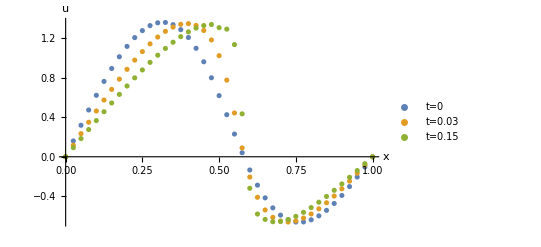

```mathematica
ListPlot[Table[Transpose[{xs2,soli[3*i]}],{i,1,6,2}],PlotLegends->{"t=0","t=0.03","t=0.15"},AxesLabel->{"x","u"}]
```

As we can see, the solution is quickly developing a steep front around  , which is precisely why the numerics for this problem suffer. In fact, if we push the solver to larger times, we will quickly find large errors in the vicinity of the front, as shown below.

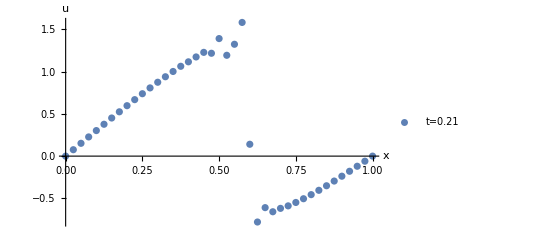

```mathematica
ListPlot[Transpose[{xs2,soli[21]}],PlotLegends->{"t=0.21"},AxesLabel->{"x","u"}]
```

### Adaptive Mesh Refinement

How can we make any progress? We use adaptive mesh refinement. In practice we want the system to automatically place its own grid points in order to better resolve any singular behaviour we might be seeing. Therefore, we promote the grid point coordinate  to a function of an internal variable  which will dictate where the grid point should be placed on the line. Mathematically, this amounts to a coordinate transformation of our system, and therefore we have to change the original equation accordingly. In the new coordinates, our equation becomes

where the subscript  denotes differentiation w.r.t .

We might think we are done since we can simply apply the Runge-Kutta procedure again on this equation and solve for , but we are missing a key ingredient, namely , i.e. how the coordinate grid points evolve in time. For this , we need an additional equation

along with the boundary conditions  The function  is called the mesh density function, its purpose is to control the concentration density of the mesh. The parameter  controls how fast the mesh adjustments happen in time. This parameter is the second parameter we are free to choose.

We almost have all the ingredients we need to solve the system, all that is left is to specify . A lot of theory behind adaptive mesh refinement is based on how to appropriately select this function. I refer the reader to reference (1) for the details. For the purposes of our discussion, we take

with  the intensity parameter given by

and Abs denotes the absolute value.

Now we are ready, given an initial  and  we can simultaneously evolve them using our RK procedure. Let us see how this works out. First, we need to redefine our basic ingredients, just as before.

```mathematica
{ξs2,hξ}=Grid1D[{1.,41}]
```

{{0.,0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9,0.925,0.95,0.975,1.},0.025}

```mathematica
D2ξ=NDSolve`FiniteDifferenceDerivative[Derivative[2],ξs2,"DifferenceOrder"->2]["DifferentiationMatrix"];
Dξ=NDSolve`FiniteDifferenceDerivative[Derivative[1],ξs2,"DifferenceOrder"->2]["DifferentiationMatrix"];
```

We must now modify our r.h.s operator to include the Adaptive Mesh procedure

```mathematica
Nx=41.;τ=10^-2;
```

```mathematica
Eqtot[{seed1_,seed2_}]:=Block[{opu1,opu2,opx1,opx2,α1,α2,ρ1,ρ2,ρsmooth,ρsmooth1,ρsmoothN},

α1=Max[Append[{Total[(Dξ.seed2)*hξ*Abs[(1/(Dξ.seed2)^2)(((-1)/(Dξ.seed2))(D2ξ.seed2)*(Dξ.seed1)+D2ξ.seed1)]^(2/3)]^3},1]]//N;

ρ1=(1+(1/α1)Abs[(1/(Dξ.seed2)^2)(((-1)/(Dξ.seed2))(D2ξ.seed2)*(Dξ.seed1)+D2ξ.seed1)]^2)^(1/3);  

Do[ρsmooth=Table[(1/4)ρ1[[j-1]]+(1/2)ρ1[[j]]+(1/4)ρ1[[j+1]],{j,2,Nx-1}];
ρsmooth1=(1/2)ρ1[[1]]+(1/2)ρ1[[2]];

ρsmoothN=(1/2)ρ1[[Nx-1]]+(1/2)ρ1[[Nx]];
ρ1=Join[{ρsmooth1},ρsmooth,{ρsmoothN}];

,4];

opx1=(1/(ρ1 τ))Dξ.(ρ1*(Dξ.seed2)); 

opu1=(Dξ.seed1/Dξ.seed2)*opx1+(ϵ/Dξ.seed2)*Dξ.(Dξ.seed1/Dξ.seed2)-(1/Dξ.seed2)Dξ.((1/2)seed1^2); 

{opu1,opx1}-{opu1*boundary,opx1*boundary}

]
```

Note the small Do loop inside this operator. This is a smoothening operation on , as described in equation 1.23 of reference (1).

```mathematica
Eqtot[{uinitial,xs2}]
```

{{0.,1022.07,1698.59,1911.14,1759.17,1413.44,1012.72,640.386,338.738,127.034,13.0241,-1.39882,81.9013,257.183,512.517,824.258,1147.,1400.78,1468.21,1229.58,653.214,-118.645,-816.773,-1225.36,-1302.96,-1141.81,-865.951,-571.02,-314.186,-124.843,-16.305,7.06079,-53.2092,-189.713,-386.433,-612.816,-815.607,-915.266,-823.501,-496.702,0.},{0.,132.164,226.832,269.695,269.117,241.501,200.531,154.39,106.986,59.7858,13.0819,-33.3085,-79.648,-125.959,-171.579,-214.383,-249.523,-267.979,-256.528,-202.342,-103.893,19.1647,131.997,206.267,234.779,226.983,196.884,155.533,109.475,61.8901,14.0627,-33.5764,-80.7688,-126.858,-170.074,-206.504,-228.892,-226.35,-187.333,-107.72,0.}}

This operator now provides the r.h.s of both the equations for  and  simultaneously. All we have to do now is evolve.

```mathematica
ClearAll@RK4StepAdaptive;
RK4StepAdaptive[dt_][u_]:=
Block[{neuralNetwork=Eqtot,k1,u1,k2,u2,k3,u3,k4,u4,λ1,λ2,λ3,λ4,λnew},
k1=neuralNetwork[u];
u1=u+dt/2 k1;

k2=neuralNetwork[u1];
u2=u1+dt/2 k2;

k3=neuralNetwork[u2];
u3=u2+dt k3;

k4=neuralNetwork[u3];

u4=u+dt/6(k1+2k2+2k3+k4);
u4
]
```

```mathematica
RK4loopAdaptive[dt_,numSteps_Integer,seed_][checkpointInterval_Integer]:=
Block[{step=RK4StepAdaptive[dt],u=seed,start,lastCheckpoint,check},

start=lastCheckpoint=AbsoluteTime[];

Do[
u=step[u];
If[Mod[i,checkpointInterval]==0,
PrintTemporary["Checkpoint at step ",i,": done ",checkpointInterval," iterations in ",Round[AbsoluteTime[]-lastCheckpoint,.01]," seconds!"];

lastCheckpoint=AbsoluteTime[];
check={Eqtot[u]//Flatten//Abs//Max};
Print[check];
soli[i]=u;
];
,{i,numSteps}];
Print["Finished in ",Round[AbsoluteTime[]-start,.01]," seconds!"];
solnew=u;

]
```

```mathematica
RK4loopAdaptive[0.00001,10000,{uinitial,xs2}][1000]
```

{2.14116}

{2.39547}

{2.53414}

{2.4108}

{2.27337}

{2.13218}

{1.93863}

{1.88618}

{1.92401}

{1.91309}

Finished in 23.72 seconds!

```mathematica
RK4loopAdaptive[0.00001,500,solnew][100]
```

{4.70724}

{4.81712}

{5.22791}

{5.63145}

{6.0231}

Finished in 1.23 seconds!

Let’s plot a couple of these solutions just to check that everything is ok.

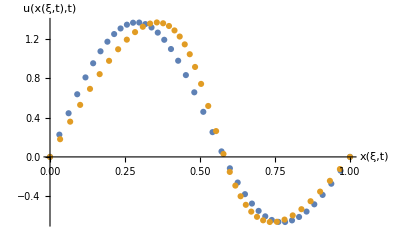

```mathematica
ListPlot[Table[Transpose[{soli[1000i]//Last,soli[1000i]//First}],{i,1,10,5}](*,PlotLegends->{"t=0","t=0.03","t=0.15"}*),AxesLabel->{"x(ξ,t)","u(x(ξ,t),t)"}]
```

What happens as we approach the singular point we encountered before? Now we see that the adaptive mesh has resolved itself to be much more dense close to the front, meaning we can resolve it without issues and push further along with time.

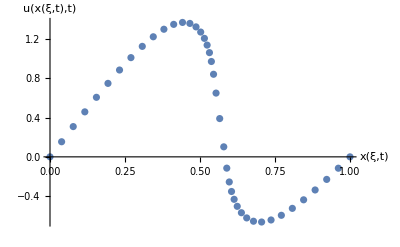

```mathematica
ListPlot[Transpose[{solnew//Last,solnew//First}](*,PlotLegends->{"t=0","t=0.03","t=0.15"}*),AxesLabel->{"x(ξ,t)","u(x(ξ,t),t)"}]
```

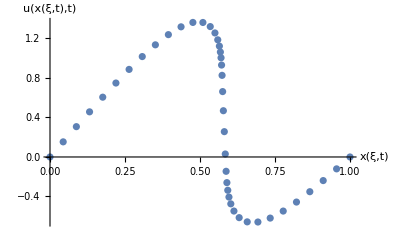

```mathematica
ListPlot[Transpose[{solnew//Last,solnew//First}](*,PlotLegends->{"t=0","t=0.03","t=0.15"}*),AxesLabel->{"x(ξ,t)","u(x(ξ,t),t)"}]
```

### Conclusions

I have implemented a simple 1d Adaptive mesh refinement algorithm to Burgers’ equation. It is clear that this algorithm allows one to improve on singular numerical procedures. A natural extension is now to include this procedure in full 3+1 dimensional simulations. This is left for further work. However, as per most 3+1 dimensional simulations, this procedure can be extremely slow running it on CPUs. Therefore I will dedicate the next section of this work to translate the above algorithm to neural network language, which allows one to use GPUs instead. It is obvious that for this particular system, just using 41 points on a line, this procedure is cumbersome and completely inefficient. In fact, it will probably lead to slower processing times. However, it is indicative of what one would have to do to use GPUs in 3+1 d, where I have seen time gains of factors of around 130x myself.

## Neural Network Implementation and GPUs

In this section I will show how to pass the above algorithm to neural network language. This involves several steps.

First, let me define some global properties of the system. This DEVICE selection is what allows us to eventually use GPUs.

```mathematica
EXECUTIONSTEPS=10;
DEVICE="GPU";
```

Next, we are going to need the equivalent of our derivative operators Dx and D2x. I obtain these by acting with convolutions on grid points of our mesh.

```mathematica
ClearAll@UFDWeights; 
UFDWeights[derOrder_Integer, kerOrder_Integer?EvenQ]:=CoefficientList[Normal[Series[ξ^(kerOrder/2)Log[ξ]^derOrder,{ξ,1,kerOrder}]/h1^derOrder],ξ]
```

```mathematica
ClearAll@NNDer1D;
NNDer1D[{lX_Real,nX_Integer}][{derOrderX_Integer,kerOrderX_Integer?EvenQ}]:=
Block[{xs,dx,xw,kernel},
{xs,dx}={xs2,hx};
xw=UFDWeights[derOrderX,kerOrderX]/.h1->dx;

kernel=TensorProduct[IdentityMatrix@1,xw];
NetChain[{
ReshapeLayer[{1,nX}],
PaddingLayer[{{0,0},{kerOrderX/2,kerOrderX/2}},Padding->"Fixed"],
ConvolutionLayer[1,{kerOrderX+1},"Biases"->None,"Weights"->kernel],
ReshapeLayer[{nX}]
},"Input"->{nX}]
]
```

Note the use of a Fixed Padding Layer at the end of our grid. This introduces a severe problem at the boundaries of our system. For example, let’s say I take the derivative of  w.r.t , i.e. the trivial operation =1. My derivative operator gives,

```mathematica
NNDer1D[{1.,41}][{1,2}]@xs2
```

{0.5,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.5}

Which is clearly wrong at the boundary points. This is the result of using a central difference convolution on a Fixed padding scheme. The problem can be fixed by defining the correct differences at the boundary points manually in Neural network language (I have done this for the full 3+1 d system for other projects, it is a hard computational problem). This is beyond the scope of this work and it turns out we can get away with this small error in what follows. However, the reader should be very careful with this issue since it can introduce large mistakes in a numerical procedure.

Next, I will define the equivalent of the Do loop smoothening function for .

```mathematica
smooth[nX_]:=NetGraph[
<|
"ρjm1"->PartLayer[;;nX-2],
"ρj"->PartLayer[2;;nX-1],
"ρjp1"->PartLayer[3;;nX],
"ρ1"->PartLayer[1],
"ρ2"->PartLayer[2],
"ρNxm1"->PartLayer[nX-1],
"ρNx"->PartLayer[nX],
"takefirst"->PartLayer[1],

"ρsmooth"->FunctionLayer@Function[{ρjm1,ρj,ρjp1},(1/4)ρjm1+(1/2)ρj+(1/4)ρjp1],
"ρsmooth1"->FunctionLayer@Function[{ρ1,ρ2},(1/2)ρ1+(1/2)ρ2],
"ρsmoothN"->FunctionLayer@Function[{ρNxm1,ρNx},(1/2)ρNxm1+(1/2)ρNx],

"joinρ"->FunctionLayer@Function[{ρsmooth1,ρsmooth,ρsmoothN},Join[{ρsmooth1},{ρsmooth},{ρsmoothN}]]

|>,
{
NetPort["Input"]->{"ρjm1","ρj","ρjp1","ρ1","ρ2","ρNxm1","ρNx"},
"ρjm1"->NetPort["ρsmooth","ρjm1"],
"ρj"->NetPort["ρsmooth","ρj"],
"ρjp1"->NetPort["ρsmooth","ρjp1"],

"ρ1"->NetPort["ρsmooth1","ρ1"],
"ρ2"->NetPort["ρsmooth1","ρ2"],

"ρNxm1"->NetPort["ρsmoothN","ρNxm1"],
"ρNx"->NetPort["ρsmoothN","ρNx"],
"ρsmooth"->NetPort["joinρ","ρsmooth"],
"ρsmooth1"->NetPort["joinρ","ρsmooth1"],
"ρsmoothN"->NetPort["joinρ","ρsmoothN"],

"joinρ"->"takefirst",

"takefirst"->NetPort["Output"]

},
"Input"->{nX}
]
```

We also need an equivalent of our boundary selector.

```mathematica
bcfunc3[nX_Integer]:=Block[{bdryX,xs,dx,v1,v2,Xboundary},
v1=ConstantArray[1,2];

     bdryX=BitOr[UnitVector[nX,1],UnitVector[nX,nX]];

Xboundary=-1*bdryX+ConstantArray[1,{nX}];

TensorProduct[v1,Xboundary]
]
```

Now we are ready to pass the full r.h.s. operator to Neural Network language. Note that I pass directly to the AMR case with both x(ξ,t) and u(x(ξ,t),t). What the below network does is just what the Eqtot operator did for us above.

```mathematica
ClearAll@NNEqs;
NNEqs[{lX_Real,nX_Integer}][kerOrderX_Integer][hξ_,τ_,ϵ_]:=

NetGraph[
<|
"x"->PartLayer[1],
"u"->PartLayer[2],
"Dξx"->NNDer1D[{lX,nX}][{1,kerOrderX}],
"D2ξx"->NNDer1D[{lX,nX}][{2,kerOrderX}],
"Dξu"->NNDer1D[{lX,nX}][{1,kerOrderX}],
"D2ξu"->NNDer1D[{lX,nX}][{2,kerOrderX}],
"Dξρ1"->NNDer1D[{lX,nX}][{1,kerOrderX}],

"α1"->FunctionLayer@Function[{Dξx,Dξu,D2ξx,D2ξu},
{Total[Dξx*hξ*Abs[1/Dξx^2((-D2ξx*Dξu)/Dξx+D2ξu)]^(2/3)]^3}],

"appα"->FunctionLayer@Function[{α},Join[α,{1}]],

"max"->FunctionLayer[Max],
"ρ1"->FunctionLayer@Function[{Dξx,Dξu,D2ξx,D2ξu,α1},(1+1/α1 Abs[1/Dξx^2((-D2ξx*Dξu)/Dξx+D2ξu)]^2)^(1/3)],

"smooth1"->NetNestOperator[smooth[nX],4],

"opx"->FunctionLayer@Function[{Dξx,D2ξx,ρ1,Dξρ1},(1/(ρ1 τ))(Dξρ1*Dξx+ρ1(D2ξx))],

"opu"->FunctionLayer@Function[{Dξx,Dξu,D2ξx,D2ξu,opx,u},(Dξu/Dξx)*opx+(ϵ/Dξx)*((Dξx*D2ξu-Dξu*D2ξx)/Dξx^2)-(1/Dξx)u*Dξu],

"catenate"->CatenateLayer[],
"reshape"->ReshapeLayer[{2,nX}],

"removebc"->FunctionLayer[(#*bcfunc3[nX])&]

|>,
{
NetPort["Input"]->{"x","u"},
"x"->{"Dξx","D2ξx"},
"u"->{"Dξu","D2ξu",NetPort["opu","u$"]},
"Dξx"->{NetPort["α1","Dξx$"],NetPort["ρ1","Dξx"],NetPort["opx","Dξx$"],NetPort["opu","Dξx$"]},
"Dξu"->{NetPort["α1","Dξu$"],NetPort["ρ1","Dξu"],NetPort["opu","Dξu$"]},
"D2ξx"->{NetPort["α1","D2ξx$"],NetPort["ρ1","D2ξx"],NetPort["opx","D2ξx$"],NetPort["opu","D2ξx$"]},
"D2ξu"->{NetPort["α1","D2ξu$"],NetPort["ρ1","D2ξu"],NetPort["opu","D2ξu$"]},

"α1"->NetPort["appα","α"],

"appα"->"max",
"max"->NetPort["ρ1","α1"],

"ρ1"->"smooth1",
"smooth1"->{"Dξρ1",NetPort["opx","ρ1$"]},
"Dξρ1"->NetPort["opx","Dξρ1$"],

"opx"->{NetPort["opu","opx$"],"catenate"},
"opu"->"catenate",

"catenate"->"reshape",
"reshape"->"removebc",

"removebc"->NetPort["Out1"]
},
"Input"->{2,nX}

]
```

Let’s see what this operator looks like in Neural Network language

```mathematica
NNEqs[{1.,41}][2][hx,0.01,0.0001]
```

NetGraph[<>]

What do we see? I have a network where I feed it one input, a vector of (u,x), and it gives me one output, the evaluation of the r.h.s of the (, ) equation with the appropriate boundary conditions. All we need now is the Runge Kutta evolution algorithm.

Here is the definition of a single 4th order Runge Kutta step.

```mathematica
ClearAll@NNRK4Step;
NNRK4Step[{lX_Real,nX_Integer}][kerOrderX_Integer?EvenQ][hξ_,τ_,ϵ_][dt_Real]:=
NNRK4Step[{lX,nX}][kerOrderX][hξ,τ,ϵ][dt]=
Block[{
neuralNetwork=NNEqs[{lX,nX}][kerOrderX][hξ,τ,ϵ]
},
NetGraph[
<|
"net1"->neuralNetwork,
"u1"->FunctionLayer@Function[{u,kk1},u+dt/2 kk1],

"net2"->neuralNetwork,

"u2"->FunctionLayer@Function[{u1,kk2},u1+dt/2 kk2],

"net3"->neuralNetwork,

"u3"->FunctionLayer@Function[{u2,kk3},u2+dt kk3],

"net4"->neuralNetwork,
"u4"->FunctionLayer@Function[{u,kk1,kk2,kk3,kk4},u+dt/6(kk1+2kk2+2kk3+kk4)]

|>,
{
NetPort["Input"]->{NetPort["net1","Input"],NetPort["u1","u$"],NetPort["u4","u$"]},

"net1"->{NetPort["u1","kk1$"],NetPort["u4","kk1$"]},

"u1"->{NetPort["net2","Input"],NetPort["u2","u1$"]},

"net2"->{NetPort["u2","kk2$"],NetPort["u4","kk2$"]},

"u2"->{NetPort["net3","Input"],NetPort["u3","u2$"]},

"net3"->{NetPort["u3","kk3$"],NetPort["u4","kk3$"]},

"u3"->NetPort["net4","Input"],

"net4"->{NetPort["u4","kk4$"]},

"u4"->NetPort["Output"]

},
"Input"->{2,nX}
]
]
```

And now let’s loop this.

```mathematica
ClearAll@RK4withbc;
RK4withbc[{lX_Real,nX_Integer}][kerOrderX_Integer?EvenQ][hξ_,τ_,ϵ_][dt_Real,numSteps_Integer,seed_][checkpointInterval_Integer]/;
Mod[checkpointInterval,EXECUTIONSTEPS]==0:=
Block[{onestep,Eq,eqchecku,multistep,u=seed,start,lastCheckpoint,params,check},

onestep=NNRK4Step[{lX,nX}][kerOrderX][hξ,τ,ϵ][dt];
multistep=NetNestOperator[onestep,EXECUTIONSTEPS];
state=<|"u"->u|>;

params=<|
"τ"->τ,"ϵ"->ϵ,"lX"->lX,"nX"->nX,"kerOrderX"->kerOrderX,"dt"->dt,"checkpointInterval"->checkpointInterval
|>;

start=lastCheckpoint=AbsoluteTime[];

Do[

If[Mod[i,checkpointInterval]==0,
PrintTemporary["Checkpoint at step ",i,": done ",checkpointInterval," iterations in ",Quantity[AbsoluteTime[]-lastCheckpoint,"s"]];
lastCheckpoint=AbsoluteTime[];

];
u=multistep[u,TargetDevice->DEVICE];

state=<|"u"->u|>;

,{i,0,0+numSteps,EXECUTIONSTEPS}];



Print["Finished in ",Round[AbsoluteTime[]-start,.01]," seconds!"];
]
RK4withbc[{lX_Real,nX_Integer}][kerOrderX_Integer?EvenQ][hξ_,τ_,ϵ_][dt_Real,numSteps_Integer,seed_][checkpointInterval_Integer,checkpointDir_String]:=
Print["Please make sure that checkpointInterval is divisible by EXECUTIONSTEPS!"];
```

Now we are ready to run. This will now work on your GPU provided you have a NVidia GPU and the latest drivers installed. Mathematica should install all relevant components for you, provided you have the right hardware.

```mathematica
Clear[state]
```

```mathematica
RK4withbc[{1.,41}][2][hx,0.01,0.0001][0.000001,10000,{xs2,uinitial}][1000]
```

Finished in 79.99 seconds!

```mathematica
RK4withbc[{1.,41}][2][hx,0.01,0.0001][0.000001,50000,"u"/.state][1000]
```

Finished in 384.69 seconds!

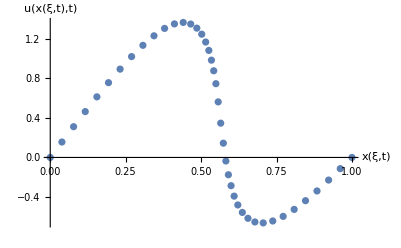

```mathematica
ListPlot[Transpose[{"u"/.state//First,"u"/.state//Last}],AxesLabel->{"x(ξ,t)","u(x(ξ,t),t)"},PlotRange->All]
```

As we can see, the Neural Network system works! It provides us with much the same answer as our previous system, however now with the ability to run on GPUs rather than CPUs.  However, there are several important points which we will discuss below.

## Conclusions

In this notebook I explored the inclusion of AMR within Neural Network language with the goal of dramatically speeding up PDE solving in any numerical physical system.  I did this just for the 1d case of Burgers’ equation, however the general architecture can be extended to any system and any dimension.  High-end numerical PDE solvers typically include gigantic clusters with several thousand CPU or GPU units, coded mostly in Fortran , C ++ or Python.  These usually involve large queue times and money investments. The ability to run large and complex numerical simulations on a single home machine would be revolutionary, and this is where my personal technological research is pointing towards. There are several important issues I want to point out which serve as take aways from this work:

1. AMR is a wonderful numerical tool to not only resolve singular places in our solution procedure, but to also speed up calculations. The idea is that since the mesh will automatically adjust itself to where it is needed, we can get away with using less but better placed points in our grid, meaning the overall system is smaller and the therefore the solution procedure faster. 

2. Using GPUs to speed up numerical computations is common practice pretty much everywhere ,including  PDE solving schemes. The standard approach is to program in CUDA directly. I have experimented with CUDALink in Wolfram, with no success.  However, the Neural Network framework in Wolfram Language is extremely powerful and can be used for PDE solving purposes, as shown above. I myself have used this architecture for full 3+1 d simulations, with insane speeds (24 hours to 10 minutes!).

3.  AMR and Neural Networks can live together, meaning those insane speeds can be made even faster. 

4. Neural Networks and GPUs do NOT always mean your numerical procedure will be faster. Be careful, the system I have shown in this notebook is a prime example. When the system is small, like most 1d systems, CPUs can work faster than this GPU adaptation. It is far from surprising, in one case one just evaluates a small vector on your CPU, while in the other one has to load a whole Neural Network on the GPU, which runs a ridiculously small vector and then has to communicate it back to the CPU, and so on... the bottom line is GPUs are needed for large systems, it is there where they really shine. 

5. The careful reader will have noted that to avoid overflowing the system, we had to pass to far smaller  time steps when going to Neural Network language. This is terrible, it makes our solver a lot slower. It is not a general feature of this architecture, but rather a specific problem introduced by the boundaries of our system and the inability of our bare differential operators to resolve them properly. We talked about this above. The Fixed padding scheme coupled with a central finite difference introduces large boundary problems which have to be treated slowly and carefully.

I hope this notebook provides the first step in the coupling of AMR with Neural Networks, with the specific target of super-speed numerical PDE solving.  The obvious extensions are:
		a) Extend the system to 3+1 dimensions. 
		b) Fix the general differential operator padding to include the correct boundary operations without the need to do so manually. 
		c) Parallelize. Can we make use of multi-GPU systems to run this even faster?

## References

(1) - Adaptive Moving Mesh Methods -  Huang and Russell  - Applied Mathematical Sciences, Vol 174 - Springer